Initializing

```mathematica
Q[t_]:=(adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t])/ada[t]-ada[t]
```

## Solving: different models

#### One

```mathematica
one[αin_, U_, Γ_, γ1_,tmax_]:=Module[
{eqns, inits, vars, sol, σ1, σ2, σ3, γ2, γ3},

(* Derived parameters *)
σ1 = (3 U)/8;
σ2 = U/2;
σ3 = -(3U)/8;
γ2 = U^2/(16 ( Γ + γ1));
γ3 = U^2/(4(Γ + γ1));

eqns = {a'[t] == (-γ1/2+ ⅈ σ1 + ⅈ σ3)a[t] + (-γ2 - γ3 + 2 ⅈ σ1)(ad[t] aa[t] + 2 a[t] ada[t] - 2 ad[t] a[t] a[t]) - γ3/2(6 ad[t] ada[t] aa[t] + 3 a[t] adad[t] aa[t] + 6 a[t] ada[t] ada[t] - 2 adad[t] a[t] a[t] a[t] - 12 ada[t] ad[t] a[t] a[t] - 6 aa[t] ad[t] ad[t] a[t] + 6 ad[t] ad[t] a[t] a[t] a[t])

,

ad'[t] == (-γ1/2 - ⅈ σ1 - ⅈ σ3)ad[t] + (-γ2 - γ3 - 2 ⅈ σ1)(2 ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) - γ3/2(6 ad[t] ada[t] ada[t] + 3 ad[t] adad[t] aa[t] + 6 a[t] adad[t] ada[t] - 6 adad[t] ad[t] a[t] a[t] - 2 aa[t] ad[t] ad[t] ad[t] - 12 ada[t] ad[t] ad[t] a[t] + 6 ad[t] ad[t] ad[t] a[t] a[t])

,

aa'[t] == (- γ1 - γ2 - γ3 + 4 ⅈ σ1 + 2 ⅈ σ3)aa[t] + (-2 γ2 - 5 γ3 + 4 ⅈ σ1)(3 ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) - γ3(3 adad[t] aa[t] aa[t] + 12 ada[t] ada[t] aa[t]- 2 adad[t]a[t] a[t] a[t] a[t] - 12 aa[t] ad[t] ad[t] a[t] a[t] - 16 ada[t] ad[t] a[t] a[t] a[t] + 16 ad[t] ad[t] a[t] a[t] a[t] a[t])

,

adad'[t] == (- γ1 - γ2 - γ3 - 4 ⅈ σ1 - 2 ⅈ σ3)adad[t] + (-2 γ2 - 5 γ3 - 4 ⅈ σ1)(3 adad[t] ada[t] - 2 ad[t] ad[t] ad[t] a[t]) - γ3(3 adad[t] adad[t] aa[t] + 12 adad[t] ada[t] ada[t] - 2 aa[t] ad[t] ad[t] ad[t] ad[t] - 12 adad[t] ad[t] ad[t] a[t] a[t] - 16 ada[t] ad[t] ad[t] ad[t] a[t] + 16 ad[t] ad[t] ad[t] ad[t] a[t] a[t])

,

ada'[t]== - γ1 ada[t] + (-2 γ2 - γ3)(adad[t] aa[t] + 2 ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) - γ3 ( 9 adad[t] ada[t] aa[t] + 6 ada[t] ada[t] ada[t] - 6 adad[t] ad[t] a[t] a[t] a[t] - 18 ada[t] ad[t] ad[t] a[t] a[t] - 6 aa[t] ad[t] ad[t] ad[t] a[t] + 16 ad[t] ad[t] ad[t] a[t] a[t] a[t])

};

inits = {
a[0] == αin,
ad[0] == Conjugate[αin],
aa[0] == αin^2,
adad[0] == Conjugate[αin]^2,
ada[0] ==Abs[αin]^2
};

vars = {a, ad, aa, adad, ada};


 NDSolve[
{eqns, inits},
vars,
{t,0,tmax},
"ExtrapolationHandler"->{Indeterminate&}
,PrecisionGoal->25, WorkingPrecision->30, AccuracyGoal->25
][[1]]

]
```

#### Two

```mathematica
stringequations2 = {"a'[t] == -0.5 γ1( a[t]) + I σ1( a[t]) + I σ3( a[t]) + (-2 I) σ5( b[t]) + (2 I) σ1( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + (2 I) σ5( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + (2 I) σ4( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + I σ5( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + I σ2( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + -I σ5( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","ad'[t] == -0.5 γ1( ad[t]) + -I σ1( ad[t]) + -I σ3( ad[t]) + (-2 I) σ1( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + -I σ5( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + (-2 I) σ5( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + -I σ2( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + (-2 I) σ4( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + I σ5( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","b'[t] == -0.5 γ2( b[t]) + I σ1( b[t]) + I σ3( b[t]) + I σ5( ad[t] aa[t] + a[t] ada[t] + a[t] ada[t] - 2 ad[t] a[t] a[t]) + I σ2( ad[t] ab[t] + a[t] adb[t] + b[t] ada[t] - 2 ad[t] a[t] b[t]) + -I σ5( ad[t] bb[t] + b[t] adb[t] + b[t] adb[t] - 2 ad[t] b[t] b[t]) + (2 I) σ4( bd[t] aa[t] + a[t] bda[t] + a[t] bda[t] - 2 bd[t] a[t] a[t]) + (-2 I) σ5( bd[t] ab[t] + a[t] bdb[t] + b[t] bda[t] - 2 bd[t] a[t] b[t]) + (2 I) σ1( bd[t] bb[t] + b[t] bdb[t] + b[t] bdb[t] - 2 bd[t] b[t] b[t])","bd'[t] == -0.5 γ2( bd[t]) + -I σ1( bd[t]) + -I σ3( bd[t]) + (2 I) σ5( ad[t]) + -I σ5( ad[t] ada[t] + ad[t] ada[t] + a[t] adad[t] - 2 ad[t] ad[t] a[t]) + (-2 I) σ4( ad[t] adb[t] + ad[t] adb[t] + b[t] adad[t] - 2 ad[t] ad[t] b[t]) + -I σ2( ad[t] bda[t] + bd[t] ada[t] + a[t] adbd[t] - 2 ad[t] bd[t] a[t]) + (2 I) σ5( ad[t] bdb[t] + bd[t] adb[t] + b[t] adbd[t] - 2 ad[t] bd[t] b[t]) + I σ5( bd[t] bda[t] + bd[t] bda[t] + a[t] bdbd[t] - 2 bd[t] bd[t] a[t]) + (-2 I) σ1( bd[t] bdb[t] + bd[t] bdb[t] + b[t] bdbd[t] - 2 bd[t] bd[t] b[t])","aa'[t] == -1. γ1( aa[t]) + (4 I) σ1( aa[t]) + (2 I) σ3( aa[t]) + (-2 I) σ5( ab[t]) + (2 I) σ4( bb[t]) + (4 I) σ1( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (4 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (4 I) σ4( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ5( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + (2 I) σ2( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-2 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t])","ada'[t] == -1. γ1( ada[t]) + (-2 I) σ5( adb[t]) + I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + -I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","adad'[t] == -1. γ1( adad[t]) + (-4 I) σ1( adad[t]) + (-2 I) σ3( adad[t]) + (-2 I) σ5( adbd[t]) + (-2 I) σ4( bdbd[t]) + (-4 I) σ1( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ5( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-4 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-2 I) σ2( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-4 I) σ4( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (2 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t])","bb'[t] == (2 I) σ4( aa[t]) + (-2 I) σ5( ab[t]) + -1. γ2( bb[t]) + (4 I) σ1( bb[t]) + (2 I) σ3( bb[t]) + (2 I) σ5( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + (2 I) σ2( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (-2 I) σ5( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (4 I) σ4( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (-4 I) σ5( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + (4 I) σ1( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","bdb'[t] == (2 I) σ5( adb[t]) + -1. γ2( bdb[t]) + -I σ5( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ4( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + I σ5( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + I σ5( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ4( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + -I σ5( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t])","bdbd'[t] == (-2 I) σ4( adad[t]) + (6 I) σ5( adbd[t]) + -1. γ2( bdbd[t]) + (-4 I) σ1( bdbd[t]) + (-2 I) σ3( bdbd[t]) + (-2 I) σ5( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + (-4 I) σ4( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + (-2 I) σ2( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (4 I) σ5( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (2 I) σ5( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + (-4 I) σ1( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])","ab'[t] == I σ5( aa[t]) + -0.5 γ1( ab[t]) + -0.5 γ2( ab[t]) + (2 I) σ1( ab[t]) + I σ2( ab[t]) + (2 I) σ3( ab[t]) + (-3 I) σ5( bb[t]) + I σ5( ada[t] aa[t] + ada[t] aa[t] + ada[t] aa[t] - 2 ad[t] a[t] a[t] a[t]) + (2 I) σ1( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ2( ada[t] ab[t] + ada[t] ab[t] + adb[t] aa[t] - 2 ad[t] a[t] a[t] b[t]) + I σ5( ada[t] bb[t] + adb[t] ab[t] + adb[t] ab[t] - 2 ad[t] a[t] b[t] b[t]) + (2 I) σ4( adb[t] bb[t] + adb[t] bb[t] + adb[t] bb[t] - 2 ad[t] b[t] b[t] b[t]) + (2 I) σ4( bda[t] aa[t] + bda[t] aa[t] + bda[t] aa[t] - 2 bd[t] a[t] a[t] a[t]) + -I σ5( bda[t] ab[t] + bda[t] ab[t] + bdb[t] aa[t] - 2 bd[t] a[t] a[t] b[t]) + (2 I) σ1( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + I σ2( bda[t] bb[t] + bdb[t] ab[t] + bdb[t] ab[t] - 2 bd[t] a[t] b[t] b[t]) + -I σ5( bdb[t] bb[t] + bdb[t] bb[t] + bdb[t] bb[t] - 2 bd[t] b[t] b[t] b[t])","adb'[t] == -0.5 γ1( adb[t]) + -0.5 γ2( adb[t]) + I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ1( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + I σ2( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (-2 I) σ5( adad[t] bb[t] + adb[t] adb[t] + adb[t] adb[t] - 2 ad[t] ad[t] b[t] b[t]) + (2 I) σ4( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (-4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ1( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + -I σ2( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (-2 I) σ4( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","bda'[t] == (2 I) σ5( ada[t]) + -0.5 γ1( bda[t]) + -0.5 γ2( bda[t]) + (-2 I) σ5( bdb[t]) + -I σ5( adad[t] aa[t] + ada[t] ada[t] + ada[t] ada[t] - 2 ad[t] ad[t] a[t] a[t]) + (-2 I) σ4( adad[t] ab[t] + ada[t] adb[t] + adb[t] ada[t] - 2 ad[t] ad[t] a[t] b[t]) + (2 I) σ1( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + -I σ2( adbd[t] aa[t] + ada[t] bda[t] + ada[t] bda[t] - 2 ad[t] bd[t] a[t] a[t]) + (4 I) σ5( adbd[t] ab[t] + ada[t] bdb[t] + adb[t] bda[t] - 2 ad[t] bd[t] a[t] b[t]) + (2 I) σ4( adbd[t] bb[t] + adb[t] bdb[t] + adb[t] bdb[t] - 2 ad[t] bd[t] b[t] b[t]) + (2 I) σ5( bdbd[t] aa[t] + bda[t] bda[t] + bda[t] bda[t] - 2 bd[t] bd[t] a[t] a[t]) + (-2 I) σ1( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + I σ2( bdbd[t] ab[t] + bda[t] bdb[t] + bdb[t] bda[t] - 2 bd[t] bd[t] a[t] b[t]) + -I σ5( bdbd[t] bb[t] + bdb[t] bdb[t] + bdb[t] bdb[t] - 2 bd[t] bd[t] b[t] b[t])","adbd'[t] == I σ5( adad[t]) + -0.5 γ1( adbd[t]) + -0.5 γ2( adbd[t]) + (-2 I) σ1( adbd[t]) + -I σ2( adbd[t]) + (-2 I) σ3( adbd[t]) + I σ5( bdbd[t]) + -I σ5( adad[t] ada[t] + adad[t] ada[t] + ada[t] adad[t] - 2 ad[t] ad[t] ad[t] a[t]) + (-2 I) σ4( adad[t] adb[t] + adad[t] adb[t] + adb[t] adad[t] - 2 ad[t] ad[t] ad[t] b[t]) + (-2 I) σ1( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + -I σ2( adad[t] bda[t] + adbd[t] ada[t] + ada[t] adbd[t] - 2 ad[t] ad[t] bd[t] a[t]) + I σ5( adad[t] bdb[t] + adbd[t] adb[t] + adb[t] adbd[t] - 2 ad[t] ad[t] bd[t] b[t]) + -I σ5( adbd[t] bda[t] + adbd[t] bda[t] + ada[t] bdbd[t] - 2 ad[t] bd[t] bd[t] a[t]) + (-2 I) σ1( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + -I σ2( adbd[t] bdb[t] + adbd[t] bdb[t] + adb[t] bdbd[t] - 2 ad[t] bd[t] bd[t] b[t]) + (-2 I) σ4( bdbd[t] bda[t] + bdbd[t] bda[t] + bda[t] bdbd[t] - 2 bd[t] bd[t] bd[t] a[t]) + I σ5( bdbd[t] bdb[t] + bdbd[t] bdb[t] + bdb[t] bdbd[t] - 2 bd[t] bd[t] bd[t] b[t])"};
```

```mathematica
two[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==αin,
b[0] ==0,
ad[0] == Conjugate[αin],
bd[0]==0,
aa[0] == αin^2,
ada[0] == Abs[αin]^2,
adad[0] ==  Conjugate[αin]^2,
bb[0] ==0, 
bdb[0]==0,
bdbd[0]==0,
ab[0]==0,
adb[0]==0,
bda[0]==0,
adbd[0]==0
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->15, WorkingPrecision->20, AccuracyGoal->15,*)
(*MaxSteps->100000*)
][[1]]


]
```

```mathematica
(* Lets me pump signal mode a instead of collective mode s_- *)
two2[αin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
inits = {
a[0]==-gb/G αin,
b[0] ==ga/G αin,
ad[0] == -gb/G Conjugate[αin],
bd[0]==ga/G Conjugate[αin],
aa[0] ==gb^2/G^2 αin^2,
ada[0] == gb^2/G^2 Abs[αin]^2,
adad[0] == gb^2/G^2 Conjugate[αin]^2,
bb[0] ==ga^2/G^2 αin^2, 
bdb[0]==ga^2/G^2 Abs[αin]^2,
bdbd[0]==ga^2/G^2 Conjugate[αin]^2,
ab[0]==(-ga gb)/G^2 αin^2,
adb[0]==(-ga gb)/G^2 Abs[αin]^2,
bda[0]==(-ga gb)/G^2 Abs[αin]^2,
adbd[0]==(-ga gb)/G^2 Conjugate[αin]^2
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->15, WorkingPrecision->20, AccuracyGoal->15,*)
(*MaxSteps->100000*)
][[1]]


]
```

```mathematica
two3[ain_, bin_, ga_, gb_, U_, γ1in_, γcin_, tmax_]:=
Module[{eqns, inits, vars,σ1in, σ2in, σ3in, σ4in, σ5in,G, γ2in, Γ, sm0, sp0},
G =√(ga^2 + gb^2);
σ1in = (U/(2G^4))(ga^4+gb^4);
σ2in = 4(U/G^4)(ga gb)^2;
σ3in = (σ2in/4)- (U/2);
σ4in = (σ2in/4);
σ5in = (U / G^4)ga gb(ga^2-gb^2);
Γ = 4 G^2/(γ1in + γcin);
γ2in = Γ + γ1in;
eqns =ToExpression[stringequations2]/.{σ1->σ1in, σ2->σ2in, σ3->σ3in, σ4->σ4in, σ5->σ5in, γ1->γ1in, γ2->γ2in};

vars = {a, b, ad, bd,aa, ada, adad, bb, bdb, bdbd, ab, adb, bda, adbd};
sp0 = (ga ain + gb bin)/G;
sm0 = (ga bin - ga ain)/G;
inits = {
a[0]==sm0,
b[0] ==sp0,
ad[0] ==Conjugate[sm0],
bd[0]==Conjugate[sp0],
aa[0] ==sm0^2,
ada[0] ==Abs[sm0]^2,
adad[0] ==Conjugate[sm0]^2,
bb[0] ==sp0^2, 
bdb[0]==Abs[sp0]^2,
bdbd[0]==Conjugate[sp0]^2,
ab[0]==sp0 sm0,
adb[0]==Conjugate[sm0] sp0,
bda[0]==Conjugate[sp0] sm0,
adbd[0]==Conjugate[sm0] * Conjugate[sp0]
};


NDSolve[
{eqns, inits},
vars,
{t, 0, tmax},
"ExtrapolationHandler"->{Indeterminate&}
(*,PrecisionGoal->33, WorkingPrecision->40, AccuracyGoal->30*)
(*,MaxSteps->1000000*)
][[1]]


]
```

#### Multi

```mathematica
(* Rules for replacing aa functions *)
aarules[nmodes_]:=Flatten[Table[
"a"<>ToString[n]<>"a"<>ToString[m]<>"[t]" -> "a"<>ToString[Min[{n,m}]]<>"a"<>ToString[Max[{n,m}]]<>"[t]"
,{n,1,nmodes},{m,1,nmodes}]];

(* Rules for replacing adad functions *)
adadrules[nmodes_]:=Flatten[Table[
"ad"<>ToString[n]<>"ad"<>ToString[m] <>"[t]"-> "ad"<>ToString[Min[{n,m}]]<>"ad"<>ToString[Max[{n,m}]]<>"[t]"
,{n,1,nmodes},{m,1,nmodes}]];

allrules[nmodes_]:= Flatten[{aarules[nmodes], adadrules[nmodes]}];


(*StringReplace along with the above rules removes degeneracy in function naming. i.e. Physically a1a2 = a2a1, but we only want to work with a1a2.*)

(* an'[t] *)
-Graphics-;

eqna[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"'[t] == (-ⅈ w"<>ToString[n]<>"- (Γ"<>ToString[n]<>"/2)) a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] -ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]]"a"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"+ 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* and'[t] *)
-Graphics-;

eqnad[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"'[t] == (ⅈ w"<>ToString[n]<>" - (Γ"<>ToString[n]<>"/2)) ad"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]]"ad"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"-2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* anan'[t] *)
-Graphics-;

eqnaa[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"a"<>ToString[n]<>"'[t] == (- 2 ⅈ w"<>ToString[n]<>" - Γ"<>ToString[n]<>" - ⅈ "<>ToString[p]<>") a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - 6 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[2 ⅈ Sum[adjacencymatrix[[n,k]]"a"<>ToString[n]<>"a"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"+ 4 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* adnan'[t] *)
(* note: nth[n] will be a function specifing the number of thermal photons in reservoir n *)
-Graphics-;

eqnada[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"a"<>ToString[n]<>"'[t] == - Γ"<>ToString[n]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + Γ"<>ToString[n]<>" nth"<>ToString[n]<>" + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "(ad"<>ToString[k]<>"a"<>ToString[n]<>"[t] - ad"<>ToString[n]<>"a"<>ToString[k]<>"[t])", {k,1,nmodes}]]
,allrules[nmodes]]
]
]
(* adnadn'[t] *)
-Graphics-;

eqnadad[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"ad"<>ToString[n]<>"'[t] == (2 ⅈ w"<>ToString[n]<>" - Γ"<>ToString[n]<>" + ⅈ "<>ToString[p]<>") ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] + 6 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + "<>ToString[2 ⅈ Sum[ adjacencymatrix[[n,k]] "ad"<>ToString[n]<>"ad"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>" - 4 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* anam'[t] *)
(*make sure that n ≠ m *)
-Graphics-;

eqnab[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"a"<>ToString[m]<>"'[t] == (-ⅈ (w"<>ToString[n]<>" + w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] a"<>ToString[m]<>"a"<>ToString[m]<>"[t] - "<>ToString[ⅈ Sum[ adjacencymatrix[[n,k]] "a"<>ToString[k]<>"a"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"-"<>ToString[ⅈ Sum[ adjacencymatrix[[m,q]] "a"<>ToString[n]<>"a"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"+ 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* andam'[t] *)
-Graphics-;

eqnadb[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes=Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"a"<>ToString[m]<>"'[t] == (ⅈ (w"<>ToString[n]<>"- w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"a"<>ToString[m]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[k]<>"a"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"-"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[n]<>"a"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* adnadm'[t] *)
-Graphics- ;

eqnadbd[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes=Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"ad"<>ToString[m]<>"'[t] == (ⅈ (w"<>ToString[n]<>"+ w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+Γ"<>ToString[m]<>")/2) ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"ad"<>ToString[m]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[k]<>"ad"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"+"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[n]<>"ad"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* adman'[t] *)
-Graphics-;

eqnbda[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[m]<>"a"<>ToString[n]<>"'[t] == (ⅈ (w"<>ToString[m]<>"-w"<>ToString[n]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[m]<>"a"<>ToString[k]<>"[t]", {k,1,nmodes}]]<>"+"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[q]<>"a"<>ToString[n]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(*Build my list of equations, given an adjacency matrix*)
buildeqlist[adjacencymatrix_]:=Module[{nmodes, eqlist1, eqlist2},
nmodes = Length[adjacencymatrix];
eqlist1 = Flatten[Table[{eqna[j, adjacencymatrix], eqnad[j, adjacencymatrix], eqnaa[j, adjacencymatrix], eqnada[j, adjacencymatrix], eqnadad[j, adjacencymatrix]}, {j,1,nmodes}]];
eqlist2=Flatten[
Table[{
eqnab[j,k, adjacencymatrix],
eqnadb[j,k, adjacencymatrix],
eqnbda[j,k, adjacencymatrix],
eqnadbd[j,k, adjacencymatrix]
},
{j,1,nmodes},{k,j+1,nmodes}
]
];(* The k range chosen in eqlist2 is to ensure that I don't form the same equation twice *)

Join[eqlist1, eqlist2] (*our list of equations*)
]

stringlistofnames[nmodes_]:=Flatten[
{
Table[
"a"<>ToString[n],{n,1,nmodes}],
Table[
"ad"<>ToString[n],{n,1,nmodes}],
Table[
"a"<>ToString[Min[{n,m}]]<>"a"<>ToString[Max[{n,m}]],
{n,1,nmodes},{m,1,nmodes}],
Table[
"ad"<>ToString[Min[{n,m}]]<>"ad"<>ToString[Max[{n,m}]],
{n,1,nmodes},{m,1,nmodes}],
Table[
"ad"<>ToString[n]<>"a"<>ToString[m],
{n,1,nmodes},{m,1,nmodes}]
}
]//DeleteDuplicates;

numberofequations[nmodes_]:=Length[stringlistofnames[nmodes]]
(*Needs the output of stringlistofnames[nmodes]*)
initialconditions[αin_,names_]:=Module[{nonzeroinits, listofzeroinits, zeroinits},
(*our only nonzero initial conditions*)
nonzeroinits={a1[0] == αin,
ad1[0] == Conjugate[αin],
a1a1[0] == αin^2,
ad1a1[0] == Abs[αin]^2,
ad1ad1[0]==Conjugate[αin]^2
};
listofzeroinits= ToExpression[Complement[names,{"a1", "ad1","a1a1", "ad1a1", "ad1ad1"}]];
(*everything else should be zero initially*)
zeroinits = (#[0]==0 )&/@listofzeroinits;

Join[nonzeroinits, zeroinits]
]

(*Needs the output of stringlistofnames[nmodes]*)
variables[names_]:=ToExpression[names]

wrep[w_,nmodes_]:=Table[ToExpression["w"<>ToString[j]]->w,{j,1,nmodes}]
Γrep[Γ_,Γn_,nmodes_]:=Join[Table[ToExpression["Γ"<>ToString[j]]->Γ,{j,1,nmodes-1}],{ToExpression["Γ"<>ToString[nmodes]] -> Γn}]
nthrep[nthermal_,nmodes_]:=Table[ToExpression["nth"<>ToString[j]]->nthermal,{j,1,nmodes}]
generalsolver[w_, U_, αin_, Γ_,Γn_, nthermal_,adjacencymatrix_,tmax_]:=
(*generalsolver[w, U, αin, Γ,Γn, nthermal,adjacencymatrix,tmax]=*)Module[{nmodes, nameslist,eqlist},
nmodes=Length[adjacencymatrix];
nameslist = stringlistofnames[nmodes];
nth[j_]:=Table[nthermal,{it,1,nmodes}][[j]];
NDSolve[
{
buildeqlist[adjacencymatrix]/.Flatten[{wrep[w,nmodes],Γrep[Γ,Γn,nmodes],nthrep[nthermal,nmodes], p->U}]

,
initialconditions[αin, nameslist]
},
variables[nameslist],
{t,0,tmax},

 (*PrecisionGoal->25, WorkingPrecision->30,AccuracyGoal->25,*)
"ExtrapolationHandler"->{Indeterminate&}
][[1]]
]
```

```mathematica
b1[g1_,g2_,t_]:=(g1 a1[t] + g2 a2[t])/(√(g1^2+g2^2));
b2[g1_,g2_,t_]:= (g1 a2[t] - g2 a1[t])/(√(g1^2+g2^2));
bd1[g1_,g2_,t_]:=(g1 ad1[t] + g2 ad2[t])/(√(g1^2+g2^2));
bd2[g1_,g2_,t_]:=(g1 ad2[t] - g2 ad1[t])/(√(g1^2+g2^2));

b1b1[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 a1a1[t] + 2 g1 g2 a1a2[t] + g2^2 a2a2[t])
bd1b1[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad1a1[t] + g1 g2 ad1a2[t] + g1 g2 ad2a1[t] + g2^2 ad2a2[t])
bd1bd1[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad1ad1[t] + 2 g1 g2 ad1ad2[t] + g2^2 ad2ad2[t])

b2b2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 a2a2[t] - 2 g1 g2 a1a2[t] + g2^2 a1a1[t])
bd2b2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad2a2[t] - g1 g2 ad1a2[t] - g1 g2 ad2a1[t] + g2^2 ad1a1[t])
bd2bd2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad2ad2[t] - 2 g1 g2 ad1ad2[t] + g2^2 ad1ad1[t])
b1b2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 a1a2[t] - g2^2 a1a2[t] - g1 g2 a1a1[t] + g1 g2 a2a2[t])
bd1b2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad1a2[t] - g1 g2 ad1a1[t] + g1 g2 ad2a2[t] - g2^2 ad2a1[t])
bd2b1[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad2a1[t] + g1 g2 ad2a2[t] - g1 g2 ad1a1[t] - g2^2 ad1a2[t])
bd1bd2[g1_,g2_,t_]:=1/(g1^2+g2^2)(g1^2 ad1ad2[t] + g1 g2 ad2ad2[t] - g1 g2 ad1ad1[t] - g2^2 ad1ad2[t])
```

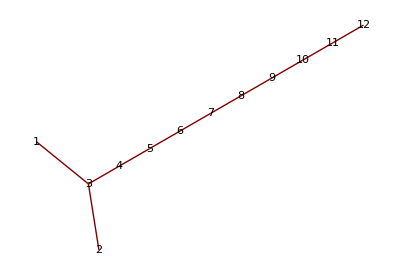

```mathematica
phogarray[g1_,g2_,g3_,nmodes_]:=
Module[{couplingQ},
Table[couplingQ[i,j]=0,{i,1,nmodes},{j,1,nmodes}];
couplingQ[1,3] = g1;
couplingQ[3,1] = g1;
couplingQ[2,3]=g2;
couplingQ[3,2]=g2;
Table[couplingQ[i,i+1]=g3,{i,4,nmodes-1}];
Table[couplingQ[i+1,i]=g3,{i,4,nmodes-1}];
Table[couplingQ[i-1,i]=g3,{i,4,nmodes-1}];
Table[couplingQ[i,i-1]=g3,{i,4,nmodes-1}];
Array[couplingQ,{nmodes,nmodes}]
]
GraphPlot[phogarray[g1,g2,g3,12],VertexLabeling->True]
thingsicareabout={a1,a2,ad1,ad2,a1a1,ad1a1,ad1ad1,a2a2,ad2a2,ad2ad2,a1a2,ad1a2,ad2a1,ad1ad2}; (*a list of the expectation values I need in order to transform into b modes. For now, these will be the ones which I export *)
```

```mathematica
(*Just a quick function to let me explore the mandel parameter. In the future I should write something more elegant (like I have in Python)*)
Qb2[g1_,g2_,t_]:= 1/bd2b2[g1,g2,t](bd2b2[g1,g2,t] bd2b2[g1,g2,t] + bd2bd2[g1,g2,t] b2b2[g1,g2,t] + bd2b2[g1,g2,t] - 2 bd2[g1,g2,t] b2[g1,g2,t] bd2[g1,g2,t] b2[g1,g2,t])-1
```

#### Multi-mode: exciting s_- instead of a

```mathematica
(* Rules for replacing aa functions *)
aarules[nmodes_]:=Flatten[Table[
"a"<>ToString[n]<>"a"<>ToString[m]<>"[t]" -> "a"<>ToString[Min[{n,m}]]<>"a"<>ToString[Max[{n,m}]]<>"[t]"
,{n,1,nmodes},{m,1,nmodes}]];

(* Rules for replacing adad functions *)
adadrules[nmodes_]:=Flatten[Table[
"ad"<>ToString[n]<>"ad"<>ToString[m] <>"[t]"-> "ad"<>ToString[Min[{n,m}]]<>"ad"<>ToString[Max[{n,m}]]<>"[t]"
,{n,1,nmodes},{m,1,nmodes}]];

allrules[nmodes_]:= Flatten[{aarules[nmodes], adadrules[nmodes]}];


(*StringReplace along with the above rules removes degeneracy in function naming. i.e. Physically a1a2 = a2a1, but we only want to work with a1a2.*)

(* an'[t] *)
-Graphics-;

eqna[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"'[t] == (-ⅈ w"<>ToString[n]<>"- (Γ"<>ToString[n]<>"/2)) a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] -ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]]"a"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"+ 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* and'[t] *)
-Graphics-;

eqnad[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"'[t] == (ⅈ w"<>ToString[n]<>" - (Γ"<>ToString[n]<>"/2)) ad"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]]"ad"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"-2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* anan'[t] *)
-Graphics-;

eqnaa[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"a"<>ToString[n]<>"'[t] == (- 2 ⅈ w"<>ToString[n]<>" - Γ"<>ToString[n]<>" - ⅈ "<>ToString[p]<>") a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - 6 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[2 ⅈ Sum[adjacencymatrix[[n,k]]"a"<>ToString[n]<>"a"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>"+ 4 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* adnan'[t] *)
(* note: nth[n] will be a function specifing the number of thermal photons in reservoir n *)
-Graphics-;

eqnada[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"a"<>ToString[n]<>"'[t] == - Γ"<>ToString[n]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + Γ"<>ToString[n]<>" nth"<>ToString[n]<>" + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "(ad"<>ToString[k]<>"a"<>ToString[n]<>"[t] - ad"<>ToString[n]<>"a"<>ToString[k]<>"[t])", {k,1,nmodes}]]
,allrules[nmodes]]
]
]
(* adnadn'[t] *)
-Graphics-;

eqnadad[n_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"ad"<>ToString[n]<>"'[t] == (2 ⅈ w"<>ToString[n]<>" - Γ"<>ToString[n]<>" + ⅈ "<>ToString[p]<>") ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] + 6 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + "<>ToString[2 ⅈ Sum[ adjacencymatrix[[n,k]] "ad"<>ToString[n]<>"ad"<>ToString[k]<>"[t]",{k,1,nmodes}]]<>" - 4 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(* anam'[t] *)
(*make sure that n ≠ m *)
-Graphics-;

eqnab[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"a"<>ToString[n]<>"a"<>ToString[m]<>"'[t] == (-ⅈ (w"<>ToString[n]<>" + w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] a"<>ToString[m]<>"a"<>ToString[m]<>"[t] - "<>ToString[ⅈ Sum[ adjacencymatrix[[n,k]] "a"<>ToString[k]<>"a"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"-"<>ToString[ⅈ Sum[ adjacencymatrix[[m,q]] "a"<>ToString[n]<>"a"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"+ 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" a"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* andam'[t] *)
-Graphics-;

eqnadb[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes=Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"a"<>ToString[m]<>"'[t] == (ⅈ (w"<>ToString[n]<>"- w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"a"<>ToString[m]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[k]<>"a"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"-"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[n]<>"a"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* adnadm'[t] *)
-Graphics- ;

eqnadbd[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes=Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[n]<>"ad"<>ToString[m]<>"'[t] == (ⅈ (w"<>ToString[n]<>"+ w"<>ToString[m]<>") - (Γ"<>ToString[n]<>"+Γ"<>ToString[m]<>")/2) ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"ad"<>ToString[m]<>"[t] + "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[k]<>"ad"<>ToString[m]<>"[t]",{k,1,nmodes}]]<>"+"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[n]<>"ad"<>ToString[q]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[n]<>"[t] ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t]"
,allrules[nmodes]]
]
]
(* adman'[t] *)
-Graphics-;

eqnbda[n_,m_,adjacencymatrix_]:=Module[{nmodes},
nmodes = Length[adjacencymatrix];
ToExpression[
StringReplace[
"ad"<>ToString[m]<>"a"<>ToString[n]<>"'[t] == (ⅈ (w"<>ToString[m]<>"-w"<>ToString[n]<>") - (Γ"<>ToString[n]<>"+ Γ"<>ToString[m]<>")/2) ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[m]<>"[t] ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] + ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"a"<>ToString[n]<>"[t] - 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"a"<>ToString[n]<>"[t] ad"<>ToString[n]<>"a"<>ToString[n]<>"[t] - ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"a"<>ToString[n]<>"[t] - "<>ToString[ⅈ Sum[adjacencymatrix[[n,k]] "ad"<>ToString[m]<>"a"<>ToString[k]<>"[t]", {k,1,nmodes}]]<>"+"<>ToString[ⅈ Sum[adjacencymatrix[[m,q]] "ad"<>ToString[q]<>"a"<>ToString[n]<>"[t]",{q,1,nmodes}]]<>"- 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"[t] ad"<>ToString[m]<>"[t] a"<>ToString[m]<>"[t] a"<>ToString[n]<>"[t] + 2 ⅈ "<>ToString[p]<>" ad"<>ToString[m]<>"[t] ad"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t] a"<>ToString[n]<>"[t]"
,allrules[nmodes]]
]
]
(*Build my list of equations, given an adjacency matrix*)
buildeqlist[adjacencymatrix_]:=Module[{nmodes, eqlist1, eqlist2},
nmodes = Length[adjacencymatrix];
eqlist1 = Flatten[Table[{eqna[j, adjacencymatrix], eqnad[j, adjacencymatrix], eqnaa[j, adjacencymatrix], eqnada[j, adjacencymatrix], eqnadad[j, adjacencymatrix]}, {j,1,nmodes}]];
eqlist2=Flatten[
Table[{
eqnab[j,k, adjacencymatrix],
eqnadb[j,k, adjacencymatrix],
eqnbda[j,k, adjacencymatrix],
eqnadbd[j,k, adjacencymatrix]
},
{j,1,nmodes},{k,j+1,nmodes}
]
];(* The k range chosen in eqlist2 is to ensure that I don't form the same equation twice *)

Join[eqlist1, eqlist2] (*our list of equations*)
]

stringlistofnames[nmodes_]:=Flatten[
{
Table[
"a"<>ToString[n],{n,1,nmodes}],
Table[
"ad"<>ToString[n],{n,1,nmodes}],
Table[
"a"<>ToString[Min[{n,m}]]<>"a"<>ToString[Max[{n,m}]],
{n,1,nmodes},{m,1,nmodes}],
Table[
"ad"<>ToString[Min[{n,m}]]<>"ad"<>ToString[Max[{n,m}]],
{n,1,nmodes},{m,1,nmodes}],
Table[
"ad"<>ToString[n]<>"a"<>ToString[m],
{n,1,nmodes},{m,1,nmodes}]
}
]//DeleteDuplicates;

numberofequations[nmodes_]:=Length[stringlistofnames[nmodes]]
(*Needs the output of stringlistofnames[nmodes]*)
initialconditions[αin_,names_, ga_, gb_]:=Module[{nonzeroinits, listofzeroinits, zeroinits, G},
(*our only nonzero initial conditions*)
G = √(ga^2 + gb^2);
nonzeroinits={a1[0] == -gb/G αin,
ad1[0] ==  (- gb)/G Conjugate[αin],
a1a1[0] == gb^2/G^2 αin^2,
ad1a1[0] == gb^2/G^2 Abs[αin]^2,
ad1ad1[0]==gb^2/G^2 Conjugate[αin]^2,
a2[0]== ga/G αin,
ad2[0]== ga/G Conjugate[αin],
a2a2[0] == ga^2/G^2 αin^2,
ad2a2[0] == ga^2/G^2 Abs[αin]^2,
ad2ad2[0] == ga^2/G^2 Conjugate[αin]^2,
a1a2[0] == (-ga gb)/G^2 αin^2,
ad1a2[0]== (-ga gb)/G^2 Abs[αin]^2,
ad2a1[0]== (-ga gb)/G^2 Abs[αin]^2,
ad1ad2[0] == (-ga gb)/G^2 Conjugate[αin]^2
};
listofzeroinits= ToExpression[Complement[names,{"a1", "ad1","a1a1", "ad1a1", "ad1ad1", "a2", "ad2", "a2a2", "ad2a2", "ad2ad2", "a1a2", "ad1a2", "ad2a1", "ad1ad2"}]];
(*everything else should be zero initially*)
zeroinits = (#[0]==0 )&/@listofzeroinits;

Join[nonzeroinits, zeroinits]
]

(*Needs the output of stringlistofnames[nmodes]*)
variables[names_]:=ToExpression[names]

wrep[w_,nmodes_]:=Table[ToExpression["w"<>ToString[j]]->w,{j,1,nmodes}]
Γrep[Γ_,Γn_,nmodes_]:=Join[Table[ToExpression["Γ"<>ToString[j]]->Γ,{j,1,nmodes-1}],{ToExpression["Γ"<>ToString[nmodes]] -> Γn}]
nthrep[nthermal_,nmodes_]:=Table[ToExpression["nth"<>ToString[j]]->nthermal,{j,1,nmodes}]
generalsolver2[w_, U_, αin_, Γ_,Γn_, nthermal_,adjacencymatrix_,tmax_]:=
(*generalsolver[w, U, αin, Γ,Γn, nthermal,adjacencymatrix,tmax]=*)Module[{nmodes, nameslist,eqlist, ga, gb},
ga = adjacencymatrix[[1,3]];
gb = adjacencymatrix[[2,3]];
nmodes=Length[adjacencymatrix];
nameslist = stringlistofnames[nmodes];
nth[j_]:=Table[nthermal,{it,1,nmodes}][[j]];
NDSolve[
{
buildeqlist[adjacencymatrix]/.Flatten[{wrep[w,nmodes],Γrep[Γ,Γn,nmodes],nthrep[nthermal,nmodes], p->U}]

,
initialconditions[αin, nameslist, ga, gb]
},
variables[nameslist],
{t,0,tmax},

(* PrecisionGoal->15, WorkingPrecision->20,AccuracyGoal->15,*)
(*PrecisionGoal->25, WorkingPrecision->30, AccuracyGoal->25,*)
"ExtrapolationHandler"->{Indeterminate&}
(*,MaxSteps->100000*)
][[1]]
]
```

## Entanglement: two-mode and multi-mode models

### Covariance matrix: multi-mode

```mathematica
v[1,1]:= 1/2+1/2 a1a1[t] + ad1a1[t] + 1/2 ad1ad1[t] - 1/2 a1[t]a1[t] - 1/2 ad1[t]ad1[t] - ad1[t] a1[t]
v[3,3] := 1/2+1/2 a2a2[t] + ad2a2[t] + 1/2 ad2ad2[t] - 1/2 a2[t] a2[t] - 1/2 ad2[t] ad2[t] - ad2[t] a2[t]
v[1,3] := 1/2 a1a2[t] + 1/2 ad1a2[t] + 1/2 ad2a1[t] + 1/2 ad1ad2[t] - 1/2 a1[t] a2[t] - 1/2 ad1[t] a2[t] - 1/2 ad2[t] a1[t] - 1/2 ad1[t] ad2[t]
v[3,1]:=1/2 a1a2[t] + 1/2 ad1a2[t] + 1/2 ad2a1[t] + 1/2 ad1ad2[t] - 1/2 a1[t] a2[t] - 1/2 ad1[t] a2[t] - 1/2 ad2[t] a1[t] - 1/2 ad1[t] ad2[t]


v[2,2] := 1/2- 1/2 a1a1[t] - 1/2 ad1ad1[t] + ad1a1[t] + 1/2 ad1[t] ad1[t] + 1/2 a1[t] a1[t] - ad1[t] a1[t]
v[4,4] := 1/2 - 1/2 a2a2[t] - 1/2 ad2ad2[t] + ad2a2[t] + 1/2 ad2[t] ad2[t] + 1/2 a2[t] a2[t] - ad2[t] a2[t]
v[2,4] := - 1/2 a1a2[t] + 1/2 ad1a2[t] + 1/2 ad2a1[t] - 1/2 ad1ad2[t] + 1/2 ad1[t] ad2[t] - 1/2 ad1[t] a2[t] - 1/2 ad2[t] a1[t] + 1/2 a1[t] a2[t]
v[4,2] :=- 1/2 a1a2[t] + 1/2 ad1a2[t] + 1/2 ad2a1[t] - 1/2 ad1ad2[t] + 1/2 ad1[t] ad2[t] - 1/2 ad1[t] a2[t] - 1/2 ad2[t] a1[t] + 1/2 a1[t] a2[t]


v[1,2] := -ⅈ/2 a1a1[t] + ⅈ/2 ad1ad1[t] + ⅈ/2 a1[t] a1[t] - ⅈ/2 ad1[t] ad1[t]
v[3,4] := - ⅈ/2 a2a2[t] + ⅈ/2 ad2ad2[t] + ⅈ/2 a2[t] a2[t] - ⅈ/2 ad2[t] ad2[t]
v[1,4]:=-ⅈ/2 a1a2[t] - ⅈ/2 ad1a2[t] + ⅈ/2 ad1ad2[t] + ⅈ/2 ad2a1[t] - ⅈ/2 a1[t] ad2[t] + ⅈ/2 a1[t] a2[t] - ⅈ/2 ad1[t] ad2[t] + ⅈ/2 ad1[t] a2[t]
v[3,2]:=-ⅈ/2 a1a2[t] + ⅈ/2 ad1a2[t] + ⅈ/2 ad1ad2[t] - ⅈ/2 ad2a1[t] - ⅈ/2 ad1[t] a2[t] + ⅈ/2 a1[t] a2[t] - ⅈ/2 ad1[t] ad2[t] + ⅈ/2 ad2[t] a1[t]

v[2,1]:=-ⅈ/2 a1a1[t] + ⅈ/2 ad1ad1[t] - ⅈ/2 ad1[t] ad1[t] + ⅈ/2 a1[t]a1[t]
v[4,3]:=-ⅈ/2 a2a2[t] + ⅈ/2 ad2ad2[t] - ⅈ/2 ad2[t]ad2[t] + ⅈ/2 a2[t]a2[t]
v[2,3]:=-ⅈ/2 a1a2[t] + ⅈ/2 ad1a2[t] + ⅈ/2 ad1ad2[t] - ⅈ/2 ad2a1[t] - ⅈ/2 ad1[t]a2[t] - ⅈ/2 ad1[t]ad2[t] + ⅈ/2 a1[t]a2[t] + ⅈ/2 a1[t]ad2[t]
v[4,1]:=-ⅈ/2 a1a2[t] - ⅈ/2 ad1a2[t] + ⅈ/2 ad1ad2[t] + ⅈ/2 ad2a1[t] - ⅈ/2 ad2[t]a1[t] - ⅈ/2 ad2[t]ad1[t] + ⅈ/2 a1[t]a2[t] + ⅈ/2 ad1[t]a2[t]
```

```mathematica
cm[τ_]:= Table[2*v[i, j], {i, 1, 4}, {j, 1, 4}]/.{t->τ};
cm//MatrixForm;
cmPT[τ_]:=2*{{v[1,1], v[1,2], v[1,3], -v[1,4]},
{v[2,1], v[2,2], v[2,3], -v[2,4]},
{v[3,1], v[3,2], v[3,3], -v[3,4]},
{-v[4,1], -v[4,2], -v[4,3], v[4,4]}}/.{t->τ};
```

### Covariance matrix: two-mode

```mathematica
rota1[g1_, g2_, t_]:=(g1 b[t] - g2 a[t])/(√(g1^2 + g2^2));
rota2[g1_, g2_, t_]:=(g2 b[t] + g1 a[t])/(√(g1^2 + g2^2));

rotad1[g1_, g2_, t_]:=(g1 bd[t] - g2 ad[t])/(√(g1^2 + g2^2));
rotad2[g1_, g2_, t_]:=(g2 bd[t] + g1 ad[t])/(√(g1^2 + g2^2));

rota1a1[g1_,g2_,t_]:=(g2^2 aa[t] - 2 g1 g2 ab[t] + g1^2 bb[t])/(g1^2 + g2^2);


rota2a2[g1_, g2_, t_]:=(g1^2 aa[t] + 2 g1 g2 ab[t]+ g2^2 bb[t])/(g1^2 + g2^2);



rotad1a1[g1_,g2_,t_]:=(g2^2 ada[t] - g1 g2 adb[t] - g1 g2 bda[t] + g1^2 bdb[t])/(g1^2 + g2^2);


rotad1ad1[g1_,g2_,t_]:=(g2^2 adad[t] - 2 g1 g2 adbd[t] + g1^2 bdbd[t])/(g1^2 + g2^2);


rotad2ad2[g1_,g2_,t_]:=(g1^2 adad[t] + 2 g1 g2 adbd[t] + g2^2 bdbd[t])/(g1^2 + g2^2);


rotad2a2[g1_,g2_,t_]:=(g1^2 ada[t] + g1 g2 adb[t] + g1 g2 bda[t] + g2^2 bdb[t])/(g1^2 + g2^2);


rota1a2[g1_,g2_,t_]:=(-g1 g2 aa[t] + g1^2 ab[t] - g2^2 ab[t] + g1 g2 bb[t])/(g1^2 + g2^2);


rotad1a2[g1_,g2_,t_]:=(-g1 g2 ada[t] - g2^2 adb[t] + g1^2 bda[t] + g1 g2 bdb[t])/(g1^2 + g2^2);


rotad2a1[g1_,g2_,t_]:=(-g1 g2 ada[t] + g1^2 adb[t] - g2^2 bda[t] + g1 g2 bdb[t])/(g1^2 + g2^2);


rotad1ad2[g1_,g2_,t_]:=(- g1 g2 adad[t] + g1^2 adbd[t] - g2^2 adbd[t] + g1 g2 bdbd[t])/(g1^2 + g2^2)
```

```mathematica
rotcm[τ_,g1_, g2_]:=Module[{rotv, t},
rotv[1,1]:= 1/2+1/2 rota1a1[g1, g2, t] +rotad1a1[g1, g2, t] + 1/2 rotad1ad1[g1, g2, t] - 1/2 rota1[g1, g2, t]rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t]rotad1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];



rotv[3,3] := 1/2+1/2 rota2a2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2ad2[g1, g2, t] - 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];


rotv[1,3] := 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];


rotv[3,1]:=1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];



rotv[2,2] := 1/2- 1/2 rota1a1[g1, g2, t] - 1/2 rotad1ad1[g1, g2, t] + rotad1a1[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];



rotv[4,4] := 1/2 - 1/2 rota2a2[g1, g2, t] - 1/2 rotad2ad2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] + 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];


rotv[2,4] := - 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t];



rotv[4,2] :=- 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t]
;



rotv[1,2] := -ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t];



rotv[3,4] := - ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t] rotad2[g1, g2, t];


rotv[1,4]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rota1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t];


rotv[3,2]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t]
;



rotv[2,1]:=-ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota1[g1, g2, t];


rotv[4,3]:=-ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t]rota2[g1, g2, t];


rotv[2,3]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rotad2[g1, g2, t];


rotv[4,1]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t];

Table[ 2 * rotv[i, j], {i, 1, 4}, {j, 1, 4}]/.{t->τ}
]
```

```mathematica
rotcmPT[τ_,g1_, g2_]:=Module[{rotv, t},
rotv[1,1]:= 1/2+1/2 rota1a1[g1, g2, t] +rotad1a1[g1, g2, t] + 1/2 rotad1ad1[g1, g2, t] - 1/2 rota1[g1, g2, t]rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t]rotad1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];
rotv[3,3] := 1/2+1/2 rota2a2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2ad2[g1, g2, t] - 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];
rotv[1,3] := 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];
rotv[3,1]:=1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] + 1/2 rotad1ad2[g1, g2, t] - 1/2 rota1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] - 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t];

rotv[2,2] := 1/2- 1/2 rota1a1[g1, g2, t] - 1/2 rotad1ad1[g1, g2, t] + rotad1a1[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota1[g1, g2, t] - rotad1[g1, g2, t] rota1[g1, g2, t];
rotv[4,4] := 1/2 - 1/2 rota2a2[g1, g2, t] - 1/2 rotad2ad2[g1, g2, t] + rotad2a2[g1, g2, t] + 1/2 rotad2[g1, g2, t] rotad2[g1, g2, t] + 1/2 rota2[g1, g2, t] rota2[g1, g2, t] - rotad2[g1, g2, t] rota2[g1, g2, t];
rotv[2,4] := - 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t];
rotv[4,2] :=- 1/2 rota1a2[g1, g2, t] + 1/2 rotad1a2[g1, g2, t] + 1/2 rotad2a1[g1, g2, t] - 1/2 rotad1ad2[g1, g2, t] + 1/2 rotad1[g1, g2, t] rotad2[g1, g2, t] - 1/2 rotad1[g1, g2, t] rota2[g1, g2, t] - 1/2 rotad2[g1, g2, t] rota1[g1, g2, t] + 1/2 rota1[g1, g2, t] rota2[g1, g2, t]
;

rotv[1,2] := -ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t];
rotv[3,4] := - ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t] rotad2[g1, g2, t];
rotv[1,4]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rota1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t];
rotv[3,2]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t] rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad2[g1, g2, t] + ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t]
;
rotv[2,1]:=-ⅈ/2 rota1a1[g1, g2, t] + ⅈ/2 rotad1ad1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t] rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota1[g1, g2, t];
rotv[4,3]:=-ⅈ/2 rota2a2[g1, g2, t] + ⅈ/2 rotad2ad2[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota2[g1, g2, t]rota2[g1, g2, t];
rotv[2,3]:=-ⅈ/2 rota1a2[g1, g2, t] + ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] - ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t] - ⅈ/2 rotad1[g1, g2, t]rotad2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rotad2[g1, g2, t];
rotv[4,1]:=-ⅈ/2 rota1a2[g1, g2, t] - ⅈ/2 rotad1a2[g1, g2, t] + ⅈ/2 rotad1ad2[g1, g2, t] + ⅈ/2 rotad2a1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rota1[g1, g2, t] - ⅈ/2 rotad2[g1, g2, t]rotad1[g1, g2, t] + ⅈ/2 rota1[g1, g2, t]rota2[g1, g2, t] + ⅈ/2 rotad1[g1, g2, t]rota2[g1, g2, t];

2* {{rotv[1,1], rotv[1,2], rotv[1,3], -rotv[1,4]},
{rotv[2,1], rotv[2,2], rotv[2,3], -rotv[2,4]},
{rotv[3,1], rotv[3,2], rotv[3,3], -rotv[3,4]},
{-rotv[4,1], -rotv[4,2], -rotv[4,3], rotv[4,4]}}/.{t->τ}
]
```

### Negativity

```mathematica
o2 = {{0,1}, {-1,0}};
o4 = ArrayFlatten[{{o2, 0}, {0, o2}}];
```

```mathematica
symp[t_, sol_]:=Abs[Eigenvalues[ⅈ o4 . cm[t]/.sol]]
sympPT[t_, sol_]:=Abs[Eigenvalues[ⅈ o4.cmPT[t]/.sol]]
rotsymp[t_, g1_, g2_, sol_]:=Abs[Eigenvalues[ⅈ o4.rotcm[t, g1, g2]/.sol]]
rotsympPT[t_, g1_, g2_, sol_]:=Abs[Eigenvalues[ⅈ o4.rotcmPT[t, g1, g2]/.sol]]
negativity[t_, sol_]:=-Total[Log[DeleteDuplicates[Select[sympPT[t, sol], #<1.0&], #1==#2&]]]
rotnegativity[t_, g1_, g2_, sol_]:=-Total[Log[DeleteDuplicates[Select[rotsympPT[t, g1, g2, sol], #1<1.0&], #1==#2&]]]
```

```mathematica
Unprotect[DirectedInfinity];
DirectedInfinity/:Log[0] 0.:=0;
DirectedInfinity/:Log[0] 0:=0;
Protect[DirectedInfinity];
Unprotect[Times];
Unprotect[Indeterminate];
Times/:Times[0,Indeterminate]:=0;
Times/:Times[0.,Indeterminate]:=0;
Indeterminate/:Indeterminate*0:=0
Indeterminate/:Indeterminate*0.:=0
Protect[Indeterminate];
Protect[Times];
```

Alternative method for calculating negativity - use analytic methods from Adesso2007 (PhD thesis)

```mathematica
mumin[t_, ga_, gb_, sol_]:=
Module[{cm,amat, gammat, bmat, adet, gamdet, bdet, seraliantilde, mu, rhsmin, mumin}
,
cm = rotcm[t, ga, gb]/.sol;
amat = cm[[1;;2,1;;2]];
gammat = cm[[1;;2,3;;4]];
bmat = cm[[3;;4,3;;4]];

adet = Det[amat];
gamdet = Det[gammat];
bdet = Det[bmat];

seraliantilde = adet + bdet - 2 gamdet;

mu = (Det[cm])^(-1/2);

rhsmin = seraliantilde - √(seraliantilde^2 - 4/mu^2);

mumin = √(rhsmin/2);

mumin
]

rotneg2[t_, g1_, g2_, sol_]:=
Module[
{eig1, eig2},
eig1 = mumin[t, g1, g2, sol];
eig2 = Min[{Re@eig1, 1}];
- Log[eig2]
]
```

Sandbox